```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### When does λ_TF = λ_e? Critical density when radiative processes “shut off”

```mathematica
Solve[λTF==1/me/.{Ef->(3 Pi^2 n)^(1/3)},n]
```

{{n→-me^3/(6 √(2 π) Z^(3/2) α^(3/2))},{n→me^3/(6 √(2 π) Z^(3/2) α^(3/2))}}

```mathematica
Convert[(me^3/(6 √(2 π) Z^(3/2) α^(3/2))/.{me->0.511,α->1/137,Z->6})(Mega ElectronVolt)^3*(200Mega ElectronVolt*Fermi)^-3,Centimeter^-3]
```

(1.21×10^32)/Centimeter^3

#### Plasma Frequency in relevant range of WD densities

```mathematica
Convert[((ni Z^2 e^2)/mi)^(1/2)*(200 Mega ElectronVolt*Fermi)^(3/2)/.{ni->10^29 Centimeter^-3,mi->12Giga ElectronVolt,e->0.3,Z->6},Kilo ElectronVolt]
```

0.464758 ElectronVolt Kilo

```mathematica
Convert[((n Z^2 e^2)/m)^(1/2)*(200 Mega ElectronVolt*Fermi)^(3/2)/.{n->10^32 Centimeter^-3,m->0.5 Mega ElectronVolt,e->0.3,Z->1},Mega ElectronVolt]
```

0.379473 ElectronVolt Mega

#### At what density does electron plasma freq = me?

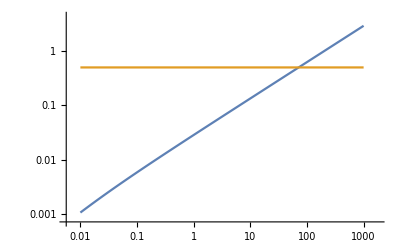

```mathematica
LogLogPlot[{(0.18 n)/(√(1+38.28312000250922 n^(2/3))),0.5},{n,0.01,1000}]
```

#### Classic EM cascades:

```mathematica
BH=(k^2/e^2+2 (1+(1-k/e)^2))/(3 k n X0);
```

```mathematica
Integrate[BH*n*k,{k,0,e}]
```

e/X0

```mathematica
PP=(1+2 ((1-e/k)^2+e^2/k^2))/(3 k n X0);
```

```mathematica
Integrate[PP,{e,0,k}]
```

7/(9 n X0)

#### LPM Energy

```mathematica
Convert[(m^2 X0 α)/(4Pi)/.X0->(4n Z^2 α^3/m^2)^-1*(200 Mega ElectronVolt*Fermi)^-3/.{m->0.511 Mega ElectronVolt,α-> 1/137,Z->6,n->10^31 Centimeter^-3},Mega ElectronVolt]
```

8.84021 ElectronVolt Mega

#### LPM Suppression

```mathematica
bremLPM=Integrate[√((Elpm k)/(e (e-k)))(k^2/e^2+2 (1+(1-k/e)^2))/(3 k n X0)*k*n,{k,0,e}];
```

```mathematica
bremLPM//N
```

(1.50535 e √(Elpm/e))/X0

```mathematica
ppLPM=Integrate[√((Elpm k)/(e (k-e)))(1+2 ((1-e/k)^2+e^2/k^2))/(3 k n X0),{e,0,k}];
```

```mathematica
ppLPM//N
```

(2.61799 √(Elpm/k))/(n X0)

#### Direct PP

```mathematica
dPPdata=Import["/Users/NewUser/Documents/Qballs/dpp.csv"];
```

```mathematica
dPP=Interpolation[dPPdata];
```

```mathematica
dPPplot=Plot[dPP[e],{e,14,26},PlotStyle->Gray];
```

InterpolatingFunction::dmval: Input value {14.0002} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Convert[300 Tera ElectronVolt,ElectronVolt]//N
```

3.×10^14 ElectronVolt

```mathematica
Convert[(e n Z^2 α^4)/m^2 10*(200 Mega ElectronVolt*Fermi)^2/.{n->10^23 Centimeter^-3,α->1/137,m->0.511 Mega ElectronVolt,Z->6},1/Meter]*Meter//N
```

0.0156545 e

```mathematica
0.015654471965760308 e*Sqrt[(3.*^14)/e]
```

```mathematica
dPPcalc=Plot[Log10[0.015654471965760308 10^e((3.*^14)/10^e)^(1/2)],{e,14,26},PlotStyle->{Thick}];
```

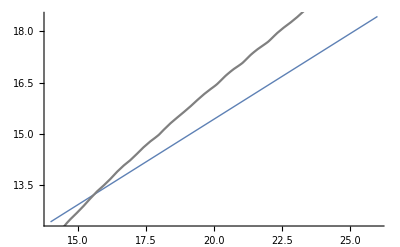

```mathematica
Show[dPPcalc,dPPplot]
```

#### eA interactions

```mathematica
eAdata=Import["/Users/NewUser/Documents/Qballs/eA.csv"];
```

```mathematica
eA=Interpolation[eAdata];
```

```mathematica
eAplot=Plot[eA[e],{e,14,26},PlotStyle->Gray];
```

InterpolatingFunction::dmval: Input value {14.0002} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Convert[e n α σγ/.{n->10^23 Centimeter^-3,σγ->1 Milli Barn,α->1/137},1/Meter]//N
```

(0.0000729927 e)/Meter

```mathematica
eAcalc=Plot[Log10[0.00007299270072992701 10^e],{e,14,26},PlotStyle->{Thick}];
```

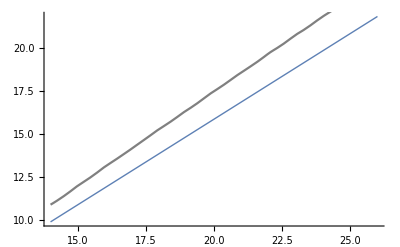

```mathematica
Show[eAcalc,eAplot]
```

#### Why is this off by O(10)?

```mathematica
Integrate[((2α)/(Pi k)(((2e-k)^2+k^2)/(2 e^2)10-1)σγ*k*n),{k,10^-5 e,e}]//N
```

7.85152 e n α σγ

#### Compare σγA with data:

```mathematica
γAdata=Import["/Users/NewUser/Documents/Qballs/gammaA.csv"];
```

```mathematica
γA=Interpolation[γAdata];
```

InterpolatingFunction::dmval: Input value {10.0002} lies outside the range of data in the interpolating function. Extrapolation will be used.

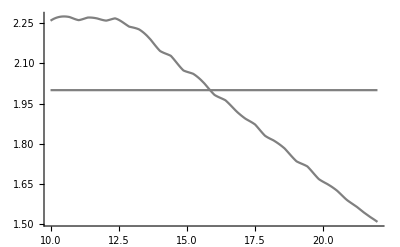

```mathematica
γAplot=Plot[{γA[e],Log10[Convert[1/(10^23 Centimeter^-3*1Milli Barn),Meter] 1/Meter]},{e,10,22},PlotStyle->Gray]
```

#### http://pdg.lbl.gov/2016/AtomicNuclearProperties/MUB/muB_carbon_graphite_C.pdf

```mathematica
Convert[e (0.5* 10^-6 Centimeter^2/Gram)(5*10^9 Gram/Centimeter^3),1/Centimeter]
```

(2500. e)/Centimeter

#### Naive calculation:

```mathematica
Convert[e n α σγ/.{α->1/137,n->10^32 Centimeter^-3,σγ->1Milli Barn},1/Centimeter]//N
```

(729.927 e)/Centimeter